```mathematica
ContarPatrones[matrices_List,patrones_List]:=Module[
{subBloques},
subBloques=Partition[#,{3,3},{1,1}]&/@matrices;
AssociationMap[
Function[
p,
Module[
{centro=p[[1]],sumaExt=p[[2]]},
Count[Flatten[#,1],b_/;b[[2,2]]===centro&&(Total[b,2]-b[[2,2]])===sumaExt]&/@subBloques]
],
patrones]
]
```

```mathematica
SeedRandom[42];
evos=ParallelTable[
CellularAutomaton[
{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},
RandomInteger[{0,1},{100,100}],
100][[2;;]]
,{i,Range[100]}];
```

```mathematica
allevos=Flatten[evos,1];
```

```mathematica
patternCount=ContarPatrones[allevos,Flatten[Table[{j,i},{i,0,8},{j,0,1}],1]];
```

```mathematica
Iconize[patternCount]
```

```mathematica
patternCount=;
```

```mathematica
names="C"<>ToString[#[[1]]]<>" N"<>ToString[#[[2]]]&/@Keys[patternCount];
total=Total[patternCount[[;;,1]]];
```

```mathematica
props=Values[patternCount]/total;propsSampled=Transpose[props]⟦1;;All;;4⟧;meansPct=(ToString[Slot["1"]]&)/@N[Mean/@Transpose[propsSampled] 100];legends=MapThread[#1<>": "<>#2<>"%"&,{names,meansPct}];
```

```mathematica
meansVec=N[Mean/@Transpose[propsSampled]] 100;
stdVec=N[StandardDeviation/@Transpose[propsSampled]] 100;
order=Ordering[meansVec,All,Greater];
namesSorted=names[[order]];
meansSorted=meansVec[[order]];
stdSorted=stdVec[[order]];
colors=If[StringStartsQ[#,"C0"],RGBColor[1, 0.8, 0.081],RGBColor[0.392, 1, 0.736]]&/@namesSorted;
n=Length[meansSorted];

lowerBound=MapThread[Max[#1-#2,0.001]&,{meansSorted,stdSorted}];
upperBound=meansSorted+stdSorted;

barChart=BarChart[meansSorted,ChartLabels->Placed[namesSorted,Axis,Rotate[#,90 Degree]&],ChartStyle->colors,PlotLabel->"Proporción de patrones (media ± std entre muestras)",ScalingFunctions->"Log"];

errorBars=Graphics[{Black,Thick,MapThread[Line[{{#1,Log[10,#2]},{#1,Log[10,#3]}}]&,{Range[n],lowerBound,upperBound}]}];

(*Etiquetas verticales,rotadas 90 grados,ancladas a la izquierda del punto*)
valueLabels=Graphics[{Black,MapThread[Text[ToString[NumberForm[#2,{Infinity,3}]]<>"%",{#1,Log[10,#3]+0.1},{-1,0},{0,1}  (*dirección del texto:vertical hacia arriba*)]&,{Range[n],meansSorted,upperBound}]}];

fplot=Show[barChart,errorBars,valueLabels,PlotRange->All,ImageSize->400,PlotRangeClipping->False,ImagePadding->{{20,1},{30,10}}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["./../../../Documentation/img/life_pattern_count.png",fplot]
```

./../../../Documentation/img/life_pattern_count.png

```mathematica
count=Counts[Flatten[#]]&/@allevos;
```

```mathematica
count[[;;3]]
```

{<|0→7214,1→2786|>,<|1→2613,0→7387|>,<|0→7468,1→2532|>}

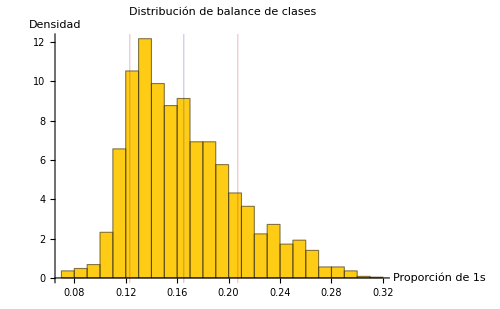

```mathematica
prop1=(#[1]/(#[0]+#[1]))&/@datos;
media=N[Mean[prop1]];
std=N[StandardDeviation[prop1]];

fplot=Histogram[prop1,Automatic,"PDF",ColorFunction->Function[{y}, RGBColor[1, 0.8, 0.081]],
GridLines->{{
{media,Directive[RGBColor[0, 0.107, 0.707],Thick]},
{media-std,Directive[RGBColor[0.707, 0, 0.128],Thick]},
{media+std,Directive[RGBColor[0.707, 0, 0.128],Thick]}},None},
AxesLabel->{"Proporción de 1s","Densidad"},PlotLabel->"Distribución de balance de clases",
PlotLegends->{"Media"<>ToString[NumberForm[media,{Infinity,3}]],"Verde = media ± std"},
ImageSize->500]
```

```mathematica
prop1=(#[1]/(#[0]+#[1]))&/@datos;
media=N[Mean[prop1]];
std=N[StandardDeviation[prop1]];

colorMedia=RGBColor[0,0.107,0.707];
colorStd=RGBColor[0.707,0,0.128];

fplot=Histogram[prop1,Automatic,"PDF",ColorFunction->Function[{y},RGBColor[1,0.8,0.081]],GridLines->{{{media,Directive[colorMedia,Thick]},{media-std,Directive[colorStd,Thick]},{media+std,Directive[colorStd,Thick]}},None},AxesLabel->{"Proporción de 1s","Densidad"},PlotLabel->"Distribución de balance de clases",ImageSize->500];

legend=LineLegend[{Directive[colorMedia,Thick],Directive[colorStd,Thick]},{"Media = "<>ToString[NumberForm[media,{Infinity,3}]],"Media ± std = "<>ToString[NumberForm[media-std,{Infinity,3}]]<>" / "<>ToString[NumberForm[media+std,{Infinity,3}]]}];

fplot=Legended[fplot,Placed[legend,{0.99,0.55}]];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["./../../../Documentation/img/life_state_distribution.png",fplot]
```

./../../../Documentation/img/life_state_distribution.png

```mathematica
100*100
```

10000

```mathematica
d2=Count[Flatten[#],1]&/@#&/@evos;
```

```mathematica
means=Mean[d2];
```

```mathematica
fplot=ListLinePlot[d2n,ColorFunction->Function[{x,y},RGBColor[1,1-Clip[Abs[y-means[[Round[x]]]]/maxDesv,{0,1}],1-Clip[Abs[y-means[[Round[x]]]]/maxDesv,{0,1}]]],ColorFunctionScaling->False,(*---Ejes y título---*)AxesLabel->{"Paso","Proporción de 1s"},PlotLabel->"Evolución de proporción de 1s por muestra",(*---Formato general---*)PlotRange->All,ImageSize->Medium];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["./../../../Documentation/img/life_all_steps.png",fplot];
```